```mathematica
∫_0^π 1/(√(r^2+a^2-2 r a Cos[θ]))ⅆθ
```

ConditionalExpression[(2 EllipticK[(4 a r)/(a+r)^2])/(√((a+r)^2)),(Re[a/r+r/a]≥2||Re[a/r+r/a]≤-2||a/r+r/a∉ℝ)&&Re[(a+r)^2]>0]

```mathematica
∫_0^1 EllipticK[(4 a r)/(a+r)^2]/(√((a+r)^2))ⅆr
```

∫_0^1 EllipticK[(4 a r)/(a+r)^2]/(√((a+r)^2))ⅆr

```mathematica
D[EllipticK[(4 a r)/(a+r)^2]/(√((a+r)^2)), r]
```

-((a+r) EllipticK[(4 a r)/(a+r)^2])/(((a+r)^2)^(3/2))+(√((a+r)^2) (-(8 a r)/(a+r)^3+(4 a)/(a+r)^2) (EllipticE[(4 a r)/(a+r)^2]-(1-(4 a r)/(a+r)^2) EllipticK[(4 a r)/(a+r)^2]))/(8 a r (1-(4 a r)/(a+r)^2))

```mathematica
Simplify[%3]
```

```mathematica
((a+r) EllipticE[(4 a r)/(a+r)^2]+(-a+r) EllipticK[(4 a r)/(a+r)^2])/(2 (a-r) r (a+r))
```

((a+r) EllipticE[(4 a r)/(a+r)^2]+(-a+r) EllipticK[(4 a r)/(a+r)^2])/(2 (a-r) r (a+r))

```mathematica
FullSimplify[((a+r) EllipticE[(4 a r)/(a+r)^2]+(-a+r) EllipticK[(4 a r)/(a+r)^2])/(2 (a-r) r (a+r))]
```

(EllipticE[(4 a r)/(a+r)^2]/(a-r)-EllipticK[(4 a r)/(a+r)^2]/(a+r))/(2 r)

```mathematica
∫_0^1 (EllipticE[(4 a r)/(a+r)^2]/(a-r)-EllipticK[(4 a r)/(a+r)^2]/(a+r))/(2 r)ⅆr
```

∫_0^1 (EllipticE[(4 a r)/(a+r)^2]/(a-r)-EllipticK[(4 a r)/(a+r)^2]/(a+r))/(2 r)ⅆr

```mathematica
Plot3D[(EllipticE[(4 a r)/(a+r)^2]/(a-r)-EllipticK[(4 a r)/(a+r)^2]/(a+r))/(2 r),{a,0,1},{r,0,1},PlotRange->{-100,100}]
```

-Graphics3D-

```mathematica
a=0.5;∫_0^1 (EllipticE[(4 a r)/(a+r)^2]/(a-r)-EllipticK[(4 a r)/(a+r)^2]/(a+r))/(2 r)ⅆr
```

∫_0^1 (EllipticE[(2. r)/(0.5+r)^2]/(0.5-r)-EllipticK[(2. r)/(0.5+r)^2]/(0.5+r))/(2 r)ⅆr

```mathematica
Table[NIntegrate[(EllipticE[(4 a r)/(a+r)^2]/(a-r)-EllipticK[(4 a r)/(a+r)^2]/(a+r))/(2 r),{r,0,1}]+1/a^2,{a,0.01,1,0.01}]
```

{9772.85,2417.69,1071.78,1298.8,526.836,247.422,173.826,185.543,107.885,71.2749,59.4497,54.7883,51.5726,49.6251,45.2823,30.6559,4.65896,27.3758,23.8374,24.8649,32.5023,1692.86,-14.3507,78.546,1.61219,-50.7009,33.3653,-1309.5,-3.30275,3.396,5.22301,4.41561,17.5193,5.73069,1.1283,1.77252,3.6684,5.41791,7.14297,7.61158,3.69489,-5.44337,4.93695,4.46858,5.83366,10.1523,788.188,-10.6818,35.0335,-2.99943,-28.6681,14.7663,-694.131,-3.88318,-0.0642996,1.14989,0.897198,8.53202,2.,-0.521709,-0.0210852,1.22601,2.4009,3.57484,3.98896,1.67731,-3.95822,2.64328,2.43415,3.39437,6.27794,514.266,-7.21935,23.0498,-1.63996,-19.295,9.95699,-471.626,-2.58783,0.0615374,0.939347,0.80624,6.18279,1.66357,-0.0708689,0.321764,1.25088,2.13804,3.03408,3.39135,1.77769,-2.26576,2.6118,2.3345,-6.20214,-27.5052,1.91754,2.56901,3.51492,12.212}

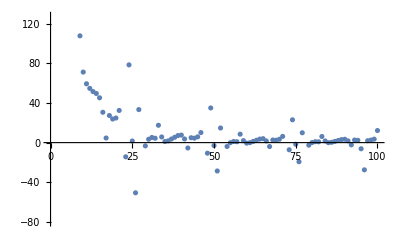

```mathematica
ListPlot[%24]
```